```mathematica
ComputeRandomVarData[distribution_,mean_,sdev_]:=Block[{p1,p2,case},
case=distribution;
Switch[case
,"NORMAL",
p1=mean;
p2=sdev;
case=1;
,"LOGNORMAL",
p2=√Log[1+(sdev/mean)^2];
p1=Log[mean ]-0.5 p2^2;
case=2;
,"DETERM",
p2=0;
p1=mean ;
case=3;
,"UNIFORME",
p1=1/2 (1+2 mean-√(1+12 sdev^2));
p2=1/2 (-1+2 mean+√(1+12 sdev^2));
case=4;
];
{mean,sdev,p1,p2,case}
];
PHI[x_]:=CDF[NormalDistribution[0,1],x];
InvPHI[x_]:=InverseCDF[NormalDistribution[0,1],x];
phi[x_]:=PDF[NormalDistribution[0,1],x];
ComputeY[RvVec_,Nsamples_]:=Block[{y,x,nrv,i,j,mu,sig,p1,p2,case},
nrv=Length[RvVec];
y=Table[0,{nrv}];
For[j=1,j≤nrv,j++,
{mu,sig,p1,p2,case}=RvVec[[j]];
y[[j]]=RandomVariate[NormalDistribution[0,1],Nsamples];
];
Transpose[y]
]
FromYtoZ[y_,Rx_]:=Block[{x,sz,i,j,var,z,Jyz,Jzy},
sz=Length[y];
{Jzy,Jyz} = ComputeJYZ[Rx];
z=Table[0,{sz}];
For[j=1,j≤sz,j++,
z[[j]]=Jyz.y[[j]];
];
z
];
FromZtoX[RvVec_,z_]:=Block[{x,sz,i,j,JXZ,JZX,MuNeqEquiv,rv,nrv,mu,sig,p1,p2,case,Fx,fx,hx},
sz=Length[z];
nrv=Length[RvVec];
x=Table[0,{sz},{nrv}];
fx=Table[0,{sz},{nrv}];
hx=Table[0,{sz},{nrv}];
For[j=1,j≤sz,j++,
For[i=1,i≤nrv,i++,
{mu,sig,p1,p2,case}=RvVec[[i]];
If[case==1,
x[[j,i]]=z[[j,i]] p2+p1 ;
];
If[case==2,
x[[j,i]]=Exp[z[[j,i]] p2+p1];
];
If[case==3,
x[[j,i]]=z[[j,i]]p1;
];
If[case==4,
Fx=CDF[UniformDistribution[{p1,p2}],z[[j,i]]];
x[[j,i]]=(p2-p1)*Fx+p1;
];
If[case≠1 && case≠2 && case≠4 && case≠3,
Print["Error Distribution not Implemented!"];
];
fx[[j,i]]=f[RvVec[[i]],x[[j,i]]];
hx[[j,i]]=phi[x[[j,i]]];
];
];
{x,fx,hx}
];
F[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case,Fx},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
Fx=CDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
Fx=CDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
Fx=If[x≥ p1,1.0,0];
,4,(*Uniforme*)
Fx=CDF[UniformDistribution[{p1,p2}],x];
(*Fx=If[x≥ p2,1.0,If[x≤ p1,0.0,(x-p1)/(p2-p1)]];*)
];
Fx
];
f[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
fx=PDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
fx=PDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
fx=If[x≥ 1.05 p1,0.0,If[x≤ 0.95 p1,0.0,10]]
,4,(*Uniforme*)
fx=PDF[UniformDistribution[{p1,p2}],x];
];
fx
];
ComputeXZ[RandonVar_,x_]:=Block[{mu,sig,z,SdevNeq,case,MuNeq,p1,p2},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
SdevNeq=sig;
MuNeq=mu;
,2,(*LogNormal*)
SdevNeq=x p2;
MuNeq=x*(1-Log[x]+p1);
,3,(*Deterministico*)
SdevNeq=1;
MuNeq=mu;
,4,(*Uniforme*)
z=InvPHI[F[RandonVar,x]];
SdevNeq=phi[z]/f[RandonVar,x];
MuNeq=x-z SdevNeq;
,5,(*Geral*)
z=InvPHI[F[RandonVar,x]];
SdevNeq=phi[z]/f[RandonVar,x];
MuNeq=x-z SdevNeq;
];
{SdevNeq,MuNeq}
];
ComputeJXZ[RandonVarVec_,x_]:=Block[{sz,i,j,JXZ,JZX,MuNeq,SdevNeq,MuNeqEquiv,Mean},
sz=Length[RandonVarVec];
JXZ=Table[0,{sz},{sz}];
JZX=Table[0,{sz},{sz}];
MuNeqEquiv=Table[0,{sz}];
Mean=Table[0,{sz}];
For[i=1,i≤sz,i++,
{SdevNeq,MuNeq}=ComputeXZ[RandonVarVec[[i]],x[[i]]];
JXZ[[i,i]]=SdevNeq;
JZX[[i,i]]=1/SdevNeq;
MuNeqEquiv[[i]]=MuNeq;
];
{JXZ,JZX,MuNeqEquiv}
];
ComputeJYZ[RX_]:=Block[{cx,L,correlated,Jyz,Jzy,NRV},
NRV=Length[RX];
If[Det[RX]≠1,
L=Transpose[CholeskyDecomposition[RX]];
Jyz=Inverse[L];
Jzy=L;
If[Det[(L.Transpose[L])-RX]> 10^-8,Print["Attention, Cholesky decomposition failed!"]];
,
Jyz=IdentityMatrix[NRV];
Jzy=IdentityMatrix[NRV];
];
Return[{Jyz,Jzy}];
];
ComputeExtremes[RandonVar_]:=Block[{xmax,xmin,mu,sig,p1,p2,case },
{mu,sig,p1,p2,case}=RandonVar;

If[case≠4,(*se for diferente de uniforme*)
xmax=mu+3sig;
xmin=mu-3sig;
,
xmin=p1;
xmax=p2;
];
{xmax,xmin}
];
FromXtoY[RvVec_,x_,Jyz_,Jzy_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,y},
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
y=Jyx.(x-Mneq);
{y,Jxy,Mneq}
];
FromYtoX[RvVec_,y_,Rx_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,x,Jyz,Jzy},
{Jyz,Jzy} =ComputeJYZ[Rx];
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
x=Jxy.y+Mneq;
{x,Jyx,Mneq}
];
```

## Cálcula matriz de rigidez de treliça

```mathematica
KE[Elast_,A_,L_]:={{Elast A/L,0,-Elast A/L,0},{0,0,0,0},{-Elast A/L,0,Elast A/L,0},{0,0,0,0}}
```

## Cálcula matriz de rotação

```mathematica
Rot[co0_,co1_]:=Block[{h,x,y,cos,sin},
x=co1[[1]]-co0[[1]];
y=co1[[2]]-co0[[2]];
h=Sqrt[x x+y y];
cos=x/h;
sin=y/h;
N[{{cos,sin,0,0},{-sin,cos,0,0},{0,0,cos,sin},{0,0,-sin,cos}}]
]
```

## Resolve treliças planas pelo método dos deslocamentos

```mathematica
Assemble[els_,nnodes_,FandPrescribedU_]:=Block[{b,h,sol={},Fe,uloc,val,Ke,i,id0,id1,nels,co,e,A,L,KG,KGE,Re,material,j,IG,k,F={},upresc={},fx,fy,ux,uy,restric={},rx,ry,FG,U},
nels=Length[els];
IG=Table[0,{4}];
KG=Table[0,{2 nnodes},{2 nnodes}];
For[i=1,i≤Length[FandPrescribedU],i++,

fx=FandPrescribedU[[i,2,1]][[1]];
fy=FandPrescribedU[[i,2,1]][[2]];
ux=FandPrescribedU[[i,2,2]][[1]];
uy=FandPrescribedU[[i,2,2]][[2]];
rx=FandPrescribedU[[i,2,3]][[1]];
ry=FandPrescribedU[[i,2,3]][[2]];
AppendTo[F,fx];
AppendTo[F,fy];
AppendTo[upresc,ux];
AppendTo[upresc,uy];

AppendTo[restric,rx];
AppendTo[restric,ry];

];

If[Length[F]≠2 nnodes,Print["Inconsistencia dos graus de liberade"]];
(*Print["F = ",F//MatrixForm];
Print["restric = ",restric//MatrixForm];*)

For[i=1,i≤nels,i++,
{id0,id1,co,material}=els[[i]];
{e,b,h,L}=material;
A=b h;
Ke=KE[e,A,L];
Re=Rot[co[[1]],co[[2]]];
KGE=Transpose[Re].Ke.Re;
(*Print[KGE//MatrixForm];*)
IG[[1]]=2(id0-1)+1;
IG[[2]]=2(id0-1)+2;
IG[[3]]=2(id1-1)+1;
IG[[4]]=2(id1-1)+2;

For[j=1,j≤4,j++,
For[k=1,k≤4,k++,
KG[[ IG[[j]],IG[[k]] ]]+= KGE[[j,k]];
];
];
];
For[j=1,j<=2 nnodes,j++,
If[Abs[restric[[j]]]<10^-7,
For[k=1,k<=2 nnodes,k++,
KG[[j,k]]=0;
KG[[k,j]]=0;
];
F[[j]]=0.;
KG[[j,j]]=1;

];
];
U=Inverse[KG].F+upresc; 
uloc=Table[0,{4}];
(*Print["U = ",U];
Print["KG = ",KG//MatrixForm];*)
For[nel=1,nel≤nels,nel++,
For[i=1,i≤2,i++,
{id0,id1,co,material}=els[[nel]];
{e,b,h,L}=material;
A=b h;
Ke=KE[e,A,L];
Re=Rot[co[[1]],co[[2]]];
uloc[[i]]=U[[2(id0-1)+i]];
uloc[[i+2]]=U[[2(id1-1)+i]];
];
uloc=Re.uloc;
Fe=Ke.uloc;
AppendTo[sol,Fe[[3]]];
(*Print["Fe = ",Fe];*)
];

sol
];
```

## -Graphics-

## -Graphics-

```mathematica
e= 68950;
free=1;
zero=0.;
b=0.265 ;
h=0.265;
f1=20;
f2=-15;
FandPrescribedU={{1,{{0,0},{0,0},{zero,zero}}},{2,{{0,0},{0,0},{free,zero}}},{3,{{0,f2},{0,0},{free,free}}},{4,{{f1,f2},{0,0},{free,free}}}};
els={{1,4,{{0,0},{0,3.05}},{e,b,h,3.05}},{4,3,{{0,3.05},{3.05,3.05}},{e,b,h,3.05}},{3,2,{{3.05,3.05}, {3.05,0}},{e,b,h,3.05}},{1,3,{{0,0},{3.05,3.05}},{e,b,h,4.31}},{4,2,{{3.05,0},{0,3.05}},{e,b,h,4.31}}};
sol=Assemble[els,4,FandPrescribedU]
```

{-15.,-20.,-35.,28.2843,7.10543×10^-15}

```mathematica
RVVec={
ComputeRandomVarData["NORMAL",172000.,0.15 172000.](*sigy*),
ComputeRandomVarData["NORMAL",68950000,0.1 68950000],(*E*)
ComputeRandomVarData["NORMAL",20.,6.],(*fx*)
ComputeRandomVarData["NORMAL",-15.,3.],(*fy*)
ComputeRandomVarData["NORMAL",0.5,0.5 0.1],
ComputeRandomVarData["NORMAL",0.15,0.15 0.1]
};
RX=IdentityMatrix[Length[RVVec]];
GXX[{X1_,X2_,X3_,X4_,X5_,X6_},mult_,bar_,nf_]:=Block[{G1,G2,x1,x0,y0,y1,L,A,inercia},
els={{1,4,{{0,0},{0,3.05}},{X2,X6,X5,3.05}},{4,3,{{0,3.05},{3.05,3.05}},{X2,X6,X5,3.05}},{3,2,{{3.05,3.05}, {3.05,0}},{X2,X6,X5,3.05}},{1,3,{{0,0},{3.05,3.05}},{X2,X6,X5,4.31}},{4,2,{{3.05,0},{0,3.05}},{X2,X6,X5,4.31}}};
sol=Assemble[els,4,{{1,{{0,0},{0,0},{zero,zero}}},{2,{{0,0},{0,0},{free,zero}}},{3,{{0,X4},{0,0},{free,free}}},{4,{{X3,X4},{0,0},{free,free}}}}];
x0=els[[bar]][[3]][[1]][[1]];
y0=els[[bar]][[3]][[1]][[2]];
x1=els[[bar]][[3]][[2]][[1]];
y1=els[[bar]][[3]][[2]][[2]];
L=Sqrt[(x1-x0)^2 + (y1-y0)^2];
A=X5 X6;
inercia=X6 X5^3/12;
G2=mult Pi^2 X2 inercia/L^2-Abs[sol[[bar]]];
G1=mult X1 A- Abs[sol[[bar]]];
(*Print["mult Pi^2 X2 ((X5 X6^3)/12)/L^2 = ",mult Pi^2 X2 ((X5 X6^3)/12)/L^2];
Print["Abs[sol[[bar]]]= ",Abs[sol[[bar]]]];
Print["L= ",L];*)
If[nf==1,
Return[G1]
,
Return[G2]
];
];
```

```mathematica
mean=Transpose[RVVec][[1]]
pt=mean
GXX[pt,1,1,1]
```

{172000.,68950000,20.,-15.,0.5,0.15}

{172000.,68950000,20.,-15.,0.5,0.15}

12885.

## Cálculo numérico do gradiente

```mathematica
ComputeGrad[fx_,pt_,nfuncs_,nf_]:=Block[{nvar,x0,x1,y0,y1,dy,dx,dydx,i,steps=10,j,x,k,xn1,xn,eps=0.0001,funcappend,Sol,var=0},
nvar=Length[pt];
Sol=Table[0,{nfuncs},{nvar}];

For[k=1,k≤nfuncs,k++,
For[i=1,i≤nvar,i++,
x0=pt[[i]]-eps;
x1=pt[[i]]+eps;

xn1=pt;
xn=pt;
x=pt;
dx=(x1-x0)/steps;
xn1[[i]]+=dx;
var=0;
For[j=1,j<=steps,j++,
var+=(fx[xn1,1,k,nf]-fx[xn,1,k,nf])/dx;
xn=xn1;
xn1=xn;
xn1[[i]]+=dx;
];
var/=steps;

Sol[[k,i]]=var;
];

];
Sol
]
```

```mathematica
FF[{x_,y_},a_,b_,c_]:={2 x^3 - 3x y^2,2 x^3 y-3y, 3 x y^2- y y}
ComputeGrad[FF,{1,2},3,1]
D[FF[{x,y},1,3,1],x]/.x->1/.y->2
```

{{{-5.9988,12.0024,12.},{-12.0006,-1.,8.0004}},{{-5.9988,12.0024,12.},{-12.0006,-1.,8.0004}},{{-5.9988,12.0024,12.},{-12.0006,-1.,8.0004}}}

{-6,12,12}

## FORM

```mathematica
RIAA[RvVec_,Rx_,lambda_,neqs_,nbars_,print_]:=Block[{ll,barss={},nlsf,lsf,bars,bar,i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=10^-3,NmaxIT=100,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alpha,xn,xmax,xmin,nrv,PostProcess={},post=False,Sdev,DistribCases,Mean},
k=1;

If[print==True,
Print["RIA"];
];
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0.,{nrv}];
xmin=Table[0.,{nrv}];
For[i=1,i≤nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
For[ll=1,ll≤neqs,ll++,
For[bar=1,bar≤nbars,bar++,
g=GXX[x,lambda,bar,ll];
k=1;
checkconv=1.;
betan=0.;
While[Abs[checkconv]>tol &&k< NmaxIT,
Gradx=ComputeGrad[GXX,x,nbars,ll];
grady=Transpose[Jxy].Gradx[[bar]];
y=((grady.y)-g)/(grady.grady)grady;
x=Jxy.y+Mneq;
If[post==True,
AppendTo[PostProcess,x];
];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=GXX[x,lambda,bar,ll];
betan1=Norm[y];
checkconv=g;
betan=betan1;
k++;

];
If[print==True,
Print["G",ll, " | bar = ",bar," | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | x = ",x ," | β = ",Norm[y]];
];
AppendTo[barss,betan];
];

];
(*Print[" SOLUTION "];
Print[" x = ",x];
Print[" β = ",betan];
Print[ " Pf = ",PHI[-betan] ];*)
(*Print[TableForm[{{"X"," β ", "PF", "Y "," α "},{x,betan,PHI[-betan] ,y,alpha}}]];*)
(*Print[TableForm[{{" X1 "," X2 ", " X3 ", " PF "," β "},{x[[1]],x[[2]],x[[3]],PHI[-betan],betan}}]];*)
Min[barss]
];
```

```mathematica
GXX[{X1_,X2_,X3_},mult_,bar_,nf_] := mult X1 X2- X3;
(*GRADX[{X1_,X2_,X3_}]:={lambda X2,lambda X1,-1};*)
```

```mathematica
RVVec={
ComputeRandomVarData["NORMAL",40.,5.]
,ComputeRandomVarData["NORMAL",50.,2.5]
,ComputeRandomVarData["NORMAL",1000.,200.]
};
RX=IdentityMatrix[Length[RVVec]];
```

```mathematica
(*tab=Table[{lambda,HRLF[RVVec,RX,lambda]},{lambda,0.05,0.2,0.01}]*)
```

```mathematica
PMA[RvVec_,Rx_,lambda_,betatarget_,neqs_,nbars_,print_]:=Block[{gxn,ll,barss={},nlsf,lsf,bars,bar,i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=10^-3,NmaxIT=30,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alpha,xn,xmax,xmin,nrv,PostProcess={},post=False,Sdev,DistribCases,Mean},
k=1;

If[print==True,
Print["PMA"];
];
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0.,{nrv}];
xmin=Table[0.,{nrv}];
For[i=1,i≤nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
For[ll=1,ll≤neqs,ll++,
For[bar=1,bar≤nbars,bar++,
g=GXX[x,lambda,bar,ll];
k=1;
checkconv=1.;
While[checkconv>tol &&k< NmaxIT,
Gradx=ComputeGrad[GXX,x,nbars,ll];
grady=Transpose[Jxy].Gradx[[bar]];
y=-betatarget grady/Norm[grady];
xn=x;
x=Jxy.y+Mneq;
If[post==True,
AppendTo[PostProcess,x];
];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
gxn=g;
g=GXX[x,lambda,bar,ll];
checkconv=Abs[Abs[g]-Abs[gxn]];
k++;


];
If[print==True,
Print["G",ll, " | bar = ",bar," | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | x = ",x ," | β = ",Norm[y]];
];
AppendTo[barss,Norm[y]];
];
];

(*Print[" SOLUTION "];
Print[" x = ",x];
Print[" β = ",betan];
Print[ " Pf = ",PHI[-betan] ];*)
(*Print[TableForm[{{"X"," β ", "PF", "Y "," α "},{x,betan,PHI[-betan] ,y,alpha}}]];*)
(*Print[TableForm[{{" X1 "," X2 ", " X3 ", " PF "," β "},{x[[1]],x[[2]],x[[3]],PHI[-betan],betan}}]];*)
Min[barss]
];
```

```mathematica
print=True;
lambda=1.;
RIAA[RVVec,RX,lambda,1,1,print]
beta=4.;
PMA[RVVec,RX,1.0,beta,1,1,print]
```

RIA

G1 | bar = 1 | iter = 5  | residual = -0.0000138498 | G(x) = -0.0000138498  | x = {28.5508,48.308,1379.23} | β = 3.04907

3.04907

PMA

G1 | bar = 1 | iter = 5  | residual = 0.000902307 | G(x) = -304.405  | x = {24.9281,48.044,1502.05} | β = 4.

4.

## Reliability Index Approximation Um line search(busca dicotômica) é utilizado para encontrar o beta target

```mathematica
FindLambdaRIA[RVVec_,RX_,lambda0_,lambda1_,betatarget_,neqs_,nbars_]:=Block[{print,ii,GXinternal,GRADXinternal,tol=10^-3,a,b,mu,lambda,erro,eps,sol,f1,f2,maxcounter=20,k=1,beta,solu},
eps=tol/10;
a=lambda0;
b=lambda1;
lambda=(a+b)*0.5-eps;
mu=(a+b)*0.5+eps;
erro =2*tol+1;
print=False;
beta=RIAA[RVVec,RX,lambda,neqs,nbars,print];
While[erro>tol && maxcounter>k,
If[beta>betatarget,
b=mu;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
beta=RIAA[RVVec,RX,lambda,neqs,nbars,print];
,
a=lambda;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
beta=RIAA[RVVec,RX,lambda,neqs,nbars,print];

];
erro=Abs[beta-betatarget];
Print[TableForm[{{"iter","β","lambda","βtarget"},{k,beta,lambda,betatarget}}]];
(*Print["mu  = ",mu];
Print["lambda  = ",lambda];
Print["beta  = ",sol[[4]]];*)
k++;
];
Print["k  = ",k];
Print["Erro  = ",erro];
sol
]
```

```mathematica
(*tab=Table[HRLF[RVVec,RX,lambda],{lambda,0,5,0.1}]*)
```

```mathematica
lambda0=0.;
lambda1=2.;
FindLambdaRIA[RVVec,RX,lambda0,lambda1,4,1,1]
```

iter | β | lambda | βtarget
1 | 4.7149 | 1.50005 | 4

iter | β | lambda | βtarget
2 | 3.98623 | 1.24998 | 4

iter | β | lambda | βtarget
3 | 4.37204 | 1.37501 | 4

iter | β | lambda | βtarget
4 | 4.18499 | 1.31249 | 4

iter | β | lambda | βtarget
5 | 4.08714 | 1.28123 | 4

iter | β | lambda | βtarget
6 | 4.03708 | 1.2656 | 4

iter | β | lambda | βtarget
7 | 4.01176 | 1.25779 | 4

iter | β | lambda | βtarget
8 | 3.99902 | 1.25388 | 4

k  = 9

Erro  = 0.000978883

{-15.,-20.1042,-35.1042,28.4317,0.}

```mathematica
print=True;
lambda=1.25418;
RIAA[RVVec,RX,lambda,1,1,print]
```

RIA

G1 | bar = 1 | iter = 10  | residual = -0.000730509 | G(x) = -0.000730509  | x = {24.9263,48.0449,1501.99} | β = 3.99999

3.99999

## -Graphics-

## -Graphics-

```mathematica
e= 68950;
free=1;
zero=0.;
b=0.265 ;
h=0.265;
f1=20;
f2=-15;
FandPrescribedU={{1,{{0,0},{0,0},{zero,zero}}},{2,{{0,0},{0,0},{free,zero}}},{3,{{0,f2},{0,0},{free,free}}},{4,{{f1,f2},{0,0},{free,free}}}};
els={{1,4,{{0,0},{0,3.05}},{e,b,h,3.05}},{4,3,{{0,3.05},{3.05,3.05}},{e,b,h,3.05}},{3,2,{{3.05,3.05}, {3.05,0}},{e,b,h,3.05}},{1,3,{{0,0},{3.05,3.05}},{e,b,h,4.31}},{4,2,{{3.05,0},{0,3.05}},{e,b,h,4.31}}};
sol=Assemble[els,4,FandPrescribedU]//Chop;
PrependTo[sol,"Normal Force (kN) "];
Print[TableForm[{{" ","barra 1","barra 2","barra 3","barra 4","barra 5"},sol}]]
```

| barra 1 | barra 2 | barra 3 | barra 4 | barra 5
Normal Force (kN)  | -15. | -20. | -35. | 28.2843 | 0

```mathematica
RVVec={
ComputeRandomVarData["NORMAL",172000.,0.15 172000.](*sigy*),
ComputeRandomVarData["NORMAL",68950000,0.1 68950000],(*E*)
ComputeRandomVarData["NORMAL",20.,6.],(*fx*)
ComputeRandomVarData["NORMAL",-15.,3.]
};
RX=IdentityMatrix[Length[RVVec]];
GXX[{X1_,X2_,X3_,X4_},mult_,bar_,nf_]:=Block[{G1,G2,x1,x0,y0,y1,L,A,inercia},
els={{1,4,{{0,0},{0,3.05}},{X2,b,h,3.05}},{4,3,{{0,3.05},{3.05,3.05}},{X2,b,h,3.05}},{3,2,{{3.05,3.05}, {3.05,0}},{X2,b,h,3.05}},{1,3,{{0,0},{3.05,3.05}},{X2,b,h,4.31}},{4,2,{{3.05,0},{0,3.05}},{X2,b,h,4.31}}};
sol=Assemble[els,4,{{1,{{0,0},{0,0},{zero,zero}}},{2,{{0,0},{0,0},{free,zero}}},{3,{{0,X4},{0,0},{free,free}}},{4,{{X3,X4},{0,0},{free,free}}}}];
L=els[[bar]][[4]][[4]];
A=b h mult;
inercia=A h^2/12;
G2= Pi^2 X2 inercia/L^2-Abs[sol[[bar]]];
G1=X1 A- Abs[sol[[bar]]];
If[nf==1,
Return[G1]
,
Return[G2]
];
];
```

```mathematica
print=True;
lambda=1.;
neeqs=1;
nbars=4;
RIAA[RVVec,RX,lambda,neeqs,nbars,print]
beta=3.71;
PMA[RVVec,RX,1.0,beta,neeqs,nbars,print]
```

RIA

G1 | bar = 1 | iter = 3  | residual = 1.46638×10^-11 | G(x) = 1.46638×10^-11  | x = {214.07,6.895×10^7,20.,-15.0331} | β = 6.65838

G1 | bar = 2 | iter = 2  | residual = -2.60702×10^-10 | G(x) = -2.60702×10^-10  | x = {286.682,6.895×10^7,20.1322,-15.} | β = 6.65559

G1 | bar = 3 | iter = 2  | residual = -7.29334×10^-9 | G(x) = -7.29334×10^-9  | x = {500.749,6.895×10^7,20.1321,-15.033} | β = 6.6473

G1 | bar = 4 | iter = 2  | residual = 7.0943×10^-9 | G(x) = 7.0943×10^-9  | x = {406.53,6.895×10^7,20.1869,-15.} | β = 6.65098

6.6473

PMA

G1 | bar = 1 | iter = 3  | residual = 9.09495×10^-13 | G(x) = 5341.89  | x = {76282.1,6.895×10^7,20.,-15.0184} | β = 3.71

G1 | bar = 2 | iter = 3  | residual = 0. | G(x) = 5336.87  | x = {76282.5,6.895×10^7,20.0737,-15.} | β = 3.71

G1 | bar = 3 | iter = 3  | residual = 0. | G(x) = 5321.86  | x = {76282.7,6.895×10^7,20.0737,-15.0184} | β = 3.71

G1 | bar = 4 | iter = 3  | residual = 1.81899×10^-12 | G(x) = 5328.55  | x = {76283.,6.895×10^7,20.1042,-15.} | β = 3.71

3.71

```mathematica
lambda0=0.1;
lambda1=0.5;
FindLambdaRIA[RVVec,RX,lambda0,lambda1,3.71,neeqs,nbars]
```

iter | β | lambda | βtarget
1 | 6.58118 | 0.20015 | 3.71

iter | β | lambda | βtarget
2 | 6.49576 | 0.150075 | 3.71

iter | β | lambda | βtarget
3 | 6.39384 | 0.125038 | 3.71

iter | β | lambda | βtarget
4 | 6.30372 | 0.112519 | 3.71

iter | β | lambda | βtarget
5 | 6.2327 | 0.106259 | 3.71

iter | β | lambda | βtarget
6 | 6.18995 | 0.10313 | 3.71

iter | β | lambda | βtarget
7 | 6.16675 | 0.101565 | 3.71

iter | β | lambda | βtarget
8 | 6.15466 | 0.100782 | 3.71

iter | β | lambda | βtarget
9 | 6.14848 | 0.100391 | 3.71

$Aborted

```mathematica
lambda=0.2;
neeqs=2;
nbars=5;
RIAA[RVVec,RX,lambda,neeqs,nbars,print]
```

RIA

G1 | bar = 1 | iter = 30  | residual = 3.81803 | G(x) = 3.81803  | x = {1265.25,6.895×10^7,20.,-15.031,0.498288,0.149486} | β = 6.61781

G1 | bar = 2 | iter = 30  | residual = -0.001973 | G(x) = -0.001973  | x = {1350.84,6.895×10^7,20.1239,-15.,0.498262,0.149479} | β = 6.61452

G1 | bar = 3 | iter = 30  | residual = -0.0232953 | G(x) = -0.0232953  | x = {2370.83,6.89499×10^7,20.1238,-15.031,0.496961,0.149088} | β = 6.57538

G1 | bar = 4 | iter = 30  | residual = 0.010208 | G(x) = 0.010208  | x = {1921.73,6.895×10^7,20.1752,-15.,0.497532,0.14926} | β = 6.59261

G1 | bar = 5 | iter = 30  | residual = 0.0440575 | G(x) = 0.0440575  | x = {2.93722,6.895×10^7,20.,-15.,0.499995,0.149999} | β = 6.66655

G2 | bar = 1 | iter = 30  | residual = 56.1853 | G(x) = 56.1853  | x = {172000.,6.5673×10^7,20.,-15.0963,0.0754572,0.14287} | β = 8.51748

G2 | bar = 2 | iter = 30  | residual = 0.0753732 | G(x) = 0.0753732  | x = {172000.,6.68359×10^7,21.014,-15.,0.0496951,0.1454} | β = 9.01812

G2 | bar = 3 | iter = 30  | residual = -0.0200965 | G(x) = -0.0200965  | x = {172000.,6.64577×10^7,20.6998,-15.175,0.0595366,0.144577} | β = 8.82505

G2 | bar = 4 | iter = 30  | residual = -0.013818 | G(x) = -0.013818  | x = {172000.,6.60311×10^7,21.3672,-15.,0.0711115,0.143649} | β = 8.60166

G2 | bar = 5 | iter = 30  | residual = 0.0784675 | G(x) = 0.0784675  | x = {172000.,6.84907×10^7,20.,-15.,0.00954001,0.149011} | β = 9.80965

6.57538

```mathematica
5 0.3
```

1.5

```mathematica
RVVec={
ComputeRandomVarData["NORMAL",5.,5 0.3](*sigy*),
ComputeRandomVarData["NORMAL",3,3 0.3]
};
RX=IdentityMatrix[Length[RVVec]];
d1=1;
d2=1;
GXX[{X1_,X2_},mult_,bar_,nf_]:=Block[{G1,G2,x1,x0,y0,y1,L,A,inercia},
1/5 mult  d1 d2 X2^2-X1
];
```

```mathematica
neeqs=1;
nbars=1;
lambda=1;
d2=5.65;
d1=5.65;
RIAA[RVVec,RX,lambda,neeqs,nbars,print]//AbsoluteTiming
```

RIA

G1 | bar = 1 | iter = 5  | residual = 0.000153241 | G(x) = 0.000153241  | x = {5.48406,0.926816} | β = 2.32603

{0.00244564,2.32603}

```mathematica
betatarget=2.32;
neeqs=1;
nbars=1;
lambda=1;
d2=5.65;
d1=5.65;
PMA[RVVec,RX,lambda,betatarget,neeqs,nbars,print]//AbsoluteTiming
```

PMA

G1 | bar = 1 | iter = 4  | residual = 0.0000965144 | G(x) = 0.0652165  | x = {5.48211,0.932135} | β = 2.32

{0.00207284,2.32}

```mathematica
lambda0=1;
lambda1=5;
neeqs=1;
nbars=1;
d1=5.65;
d2=5.65;
betatarget=2.32;
FindLambdaRIA[RVVec,RX,lambda0,lambda1,betatarget,neeqs,nbars]
```

iter | β | lambda | βtarget
1 | 3.1779 | 2.00015 | 2.32

iter | β | lambda | βtarget
2 | 2.5169 | 1.50008 | 2.32

iter | β | lambda | βtarget
3 | 2.43473 | 1.25004 | 2.32

iter | β | lambda | βtarget
4 | 2.38465 | 1.12502 | 2.32

iter | β | lambda | βtarget
5 | 2.35662 | 1.06251 | 2.32

iter | β | lambda | βtarget
6 | 2.3416 | 1.03125 | 2.32

iter | β | lambda | βtarget
7 | 2.33395 | 1.01563 | 2.32

iter | β | lambda | βtarget
8 | 2.33003 | 1.00781 | 2.32

iter | β | lambda | βtarget
9 | 2.32804 | 1.00391 | 2.32

iter | β | lambda | βtarget
10 | 2.32704 | 1.00195 | 2.32

iter | β | lambda | βtarget
11 | 2.32654 | 1.00098 | 2.32

iter | β | lambda | βtarget
12 | 2.32628 | 1.00049 | 2.32

iter | β | lambda | βtarget
13 | 2.32616 | 1.00024 | 2.32

iter | β | lambda | βtarget
14 | 2.32609 | 1.00012 | 2.32

iter | β | lambda | βtarget
15 | 2.32606 | 1.00006 | 2.32

iter | β | lambda | βtarget
16 | 2.32605 | 1.00003 | 2.32

iter | β | lambda | βtarget
17 | 2.32604 | 1.00002 | 2.32

iter | β | lambda | βtarget
18 | 2.32604 | 1.00001 | 2.32

iter | β | lambda | βtarget
19 | 2.32603 | 1. | 2.32

k  = 20

Erro  = 0.00603373

{-15.,-20.1042,-35.1042,28.4317,0.}

```mathematica
lambda0=1;
lambda1=5;
neeqs=1;
nbars=1;
d1=1;
d2=1;
betatarget=2.32;
FindLambdaRIA[RVVec,RX,lambda0,lambda1,betatarget,neeqs,nbars]
```

iter | β | lambda | βtarget
1 | 0.645676 | 4.00005 | 2.32

iter | β | lambda | βtarget
2 | 2.3718 | 4.50013 | 2.32

iter | β | lambda | βtarget
3 | 1.6519 | 4.25009 | 2.32

iter | β | lambda | βtarget
4 | 2.06838 | 4.37511 | 2.32

iter | β | lambda | βtarget
5 | 2.22922 | 4.43762 | 2.32

iter | β | lambda | βtarget
6 | 2.30246 | 4.46887 | 2.32

iter | β | lambda | βtarget
7 | 2.33758 | 4.4845 | 2.32

iter | β | lambda | βtarget
8 | 2.32014 | 4.47668 | 2.32

k  = 9

Erro  = 0.000135237

{-15.,-20.1042,-35.1042,28.4317,0.}

```mathematica
5.65 5.65
```

31.9225

```mathematica
FindRoot[{{D1^2 +D2^2==0},{D1 D2 ==4.47668}},{D1,1.2},{D2,0}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{D1→0.929589,D2→0.929591}

```mathematica
FindMinimum[D1^2 +(4.47677/D1)^2,{D1,0.1}]
```

{8.95354,{D1→2.11584}}

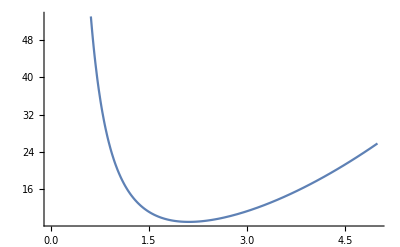

```mathematica
Plot[D1^2 +(4.47677/D1)^2,{D1,0,5}]
```

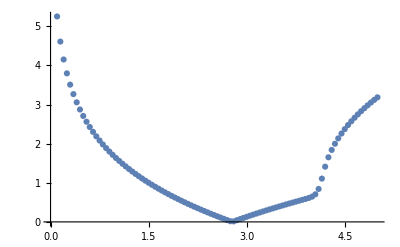

```mathematica
table=Table[{lambda,RIAA[RVVec,RX,lambda,neeqs,nbars,False]},{lambda,0.1,5,0.05}];
ListPlot[table]
```

```mathematica
PMA[RvVec_,Rx_,lambda_,betatarget_,neqs_,nbars_,print_]:=Block[{gxn,ll,barss={},nlsf,lsf,bars,bar,i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=10^-3,NmaxIT=5,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alpha,xn,xmax,xmin,nrv,PostProcess={},post=False,Sdev,DistribCases,Mean},
k=1;

If[print==True,
Print["PMA"];
];
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0.,{nrv}];
xmin=Table[0.,{nrv}];
For[i=1,i≤nrv,i++,{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]]];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
For[ll=1,ll≤neqs,ll++,
For[bar=1,bar≤nbars,bar++,

While[checkconv>tol &&k< NmaxIT,
If[print==True,
Print["G",ll, " | bar = ",bar," | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | x = ",x ," | β = ",Norm[y]];
];

Gradx=ComputeGrad[GXX,x,nbars,ll];
grady=Transpose[Jxy].Gradx[[bar]];
alpha0=-grady/Norm[grady];
yn1=-betatarget alpha0;

betan=Norm[yn1];
x=Jxy.yn1+Mneq;
y=yn1;
{yn1,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
gxn=g;
g=GXX[x,lambda,bar,ll];

checkconv=Abs[Abs[g]-Abs[gxn]];
k++;

];

AppendTo[barss,Norm[y]];
];
];

];
```

```mathematica
RVVec={
ComputeRandomVarData["NORMAL",5.,5 0.3](*sigy*),
ComputeRandomVarData["NORMAL",3,3 0.3]
};
RX=IdentityMatrix[Length[RVVec]];
d1=1;
d2=1;
GXX[{X1_,X2_},mult_,bar_,nf_]:=Block[{G1,G2,x1,x0,y0,y1,L,A,inercia},
1/5 mult  d1 d2 X2^2-X1
];
```

```mathematica
PMA[RVVec,RX,1,2,1,1,True]
```